Definicje funkcji używanych przy mapowaniu:

```mathematica
GetMax[x_] :={First[x], Max[Take[x,{2,Length[x]}]]};
GetMean[x_] :={First[x], Mean[Take[x,{2,Length[x]}]]};
GetVariance[x_] :={First[x], Variance[Take[x,{2,Length[x]}]]};
GetPlusStandardDeviation[x_] :={First[x],Mean[Take[x,{2,Length[x]}]] + StandardDeviation[Take[x,{2,Length[x]}]]};
GetMinusStandardDeviation[x_] :={First[x],Mean[Take[x,{2,Length[x]}]] - StandardDeviation[Take[x,{2,Length[x]}]]};
```

```mathematica
UNI :="uniform"; MIN := "minimize"; AGL := "always_go_left";
Strategies := {UNI, MIN, AGL};
CCP := "coupon_collector"; BPP := "birthday_paradox"; MLP := "max_load";
Problems := {CCP, BPP, MLP};
RawResults[s_,p_,d_] := ReadList[StringJoin["/home/dev/Workspaces/Studies/AnalAlgo/BallsAndCups/cups_" ,s,"_",p,"_",ToString[d],".m"], Number, RecordLists->True];
ResultsMax[s_,p_,d_] := Map[GetMax, RawResults[s,p,d]];
ResultsMean[s_,p_,d_] := Map[GetMean,  RawResults[s,p,d]];
ResultsVariance[s_,p_,d_] := Map[GetVariance,  RawResults[s,p,d]];
ResultsPlusStandardDeviation[s_,p_,d_] := Map[GetPlusStandardDeviation,  RawResults[s,p,d]];
ResultsMinusStandardDeviation[s_,p_,d_] := Map[GetMinusStandardDeviation,  RawResults[s,p,d]];
```

Wyświetlanie wyników dla Coupon Collector Problem:

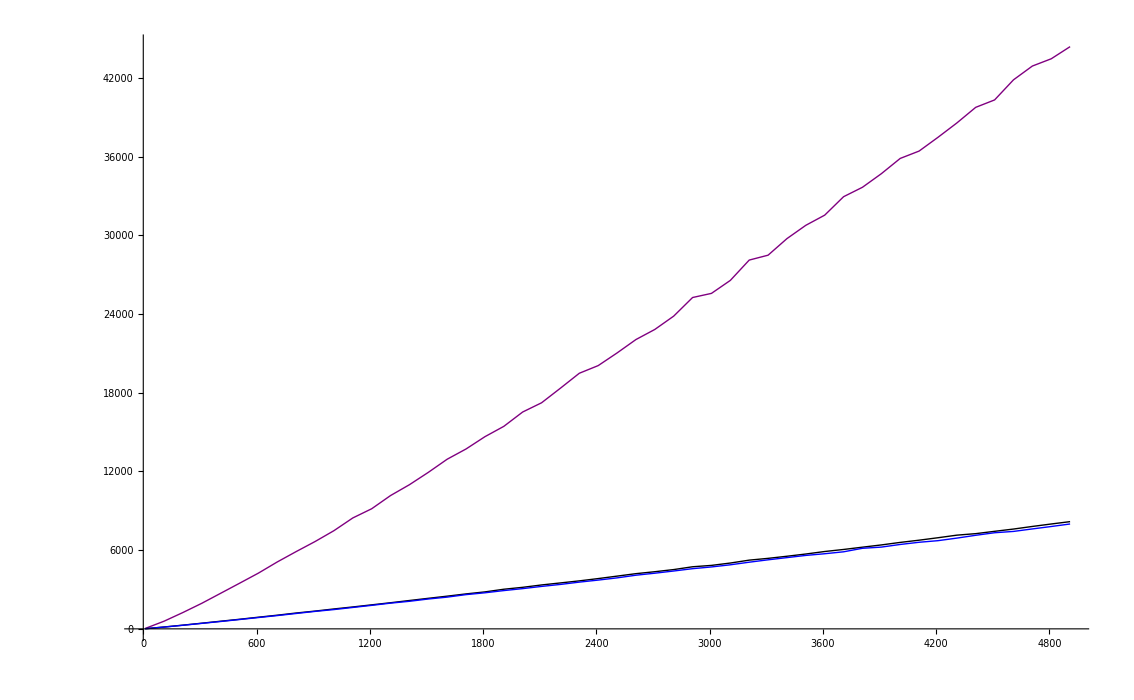

```mathematica
Show[
ListLinePlot[ResultsMean[UNI,CCP,10],PlotStyle->Purple],
ListLinePlot[ResultsMean[MIN,CCP,10],PlotStyle -> Black],
ListLinePlot[ResultsMean[AGL,CCP,10],PlotStyle -> Blue]
]
```

Wyświetlanie wyników dla Birthday Paradox Problem:

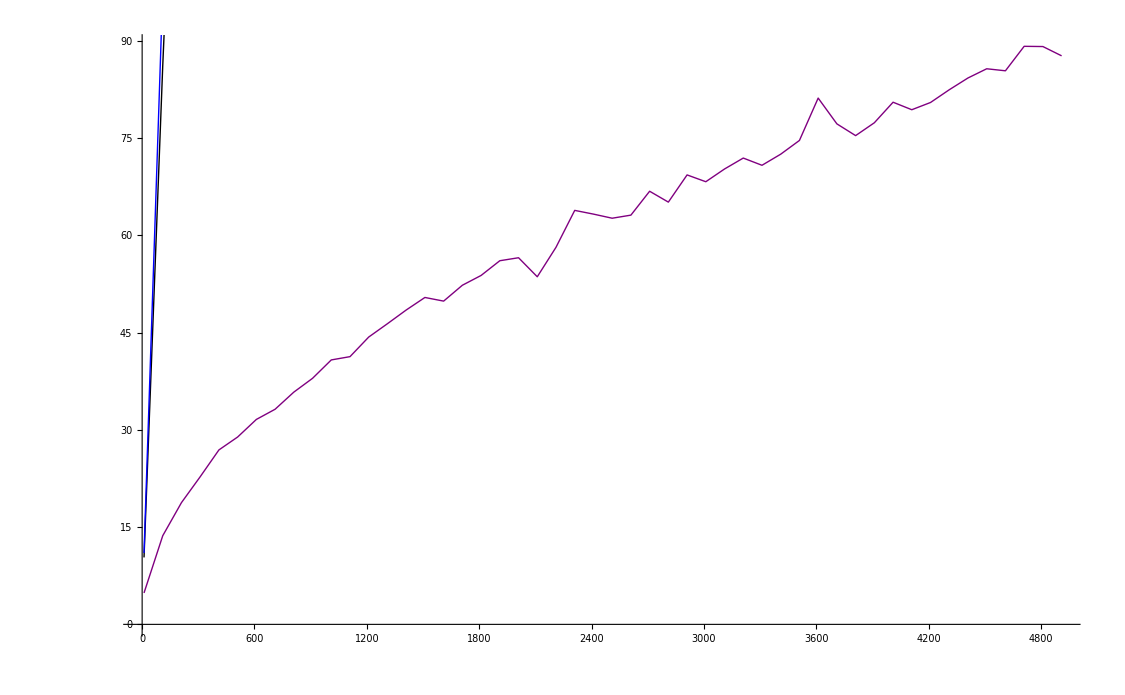

```mathematica
Show[
ListLinePlot[ResultsMean[UNI,BPP,10],PlotStyle->Purple],
ListLinePlot[ResultsMean[MIN,BPP,10],PlotStyle -> Black],
ListLinePlot[ResultsMean[AGL,BPP,10],PlotStyle -> Blue]
]
```

Wyświetlanie wyników dla Max Load Problem:

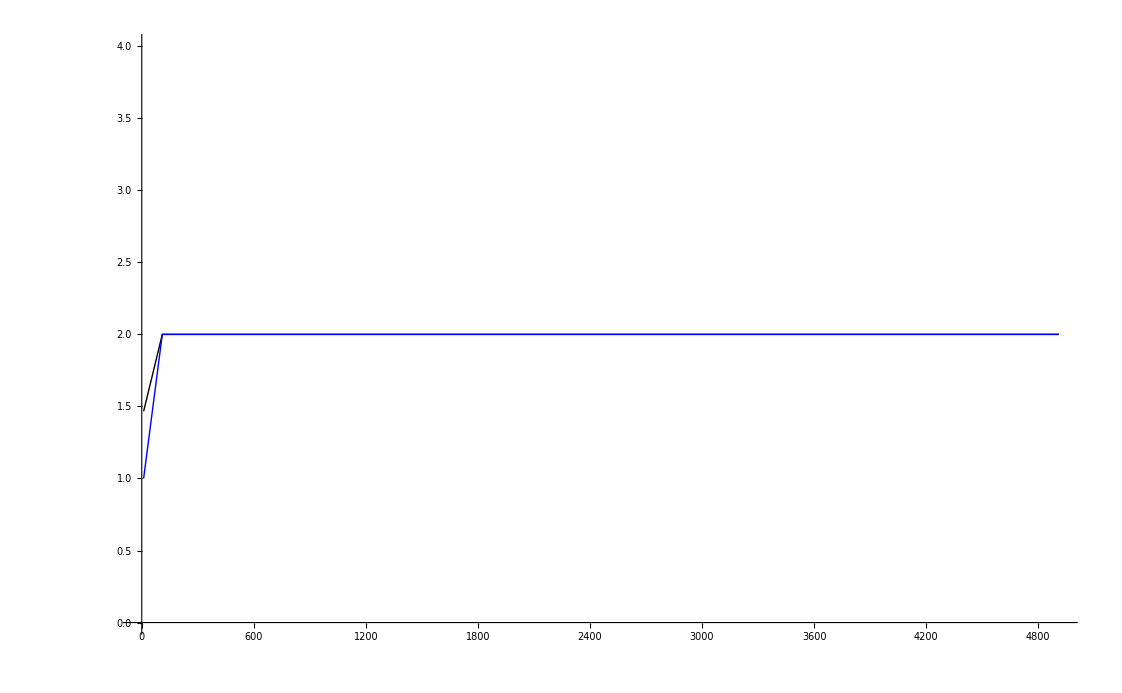

```mathematica
Show[
ListLinePlot[ResultsMean[MIN,MLP,10],PlotStyle -> Black],
ListLinePlot[ResultsMean[AGL,MLP,10],PlotStyle -> Blue]
]
```

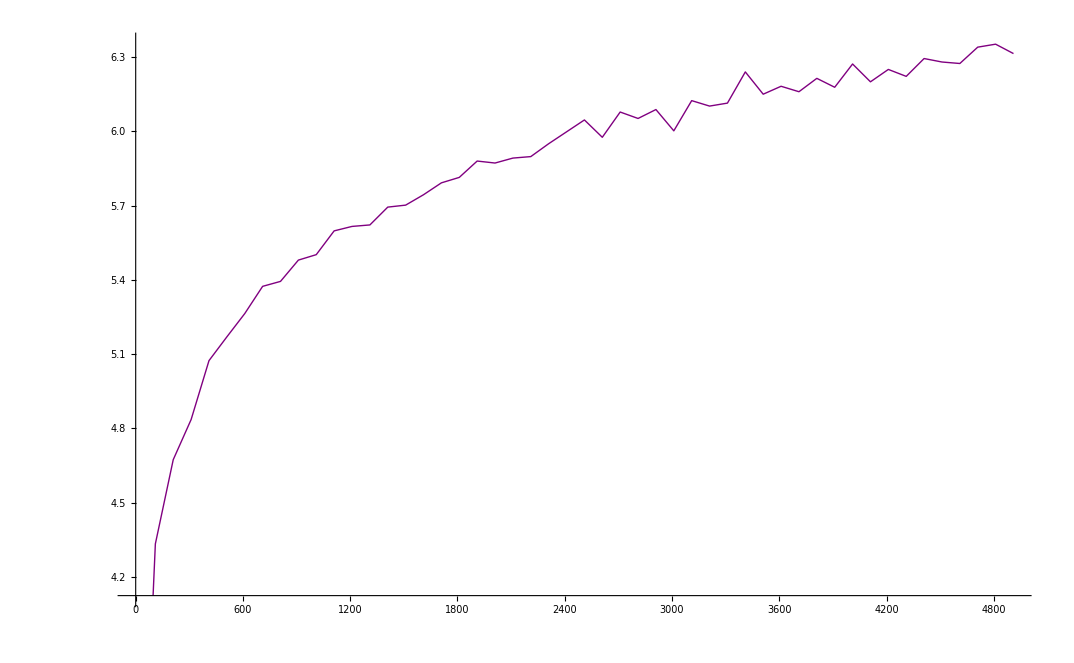

```mathematica
ListLinePlot[ResultsMean[UNI,MLP,10],PlotStyle->Purple]
```